## 6 | Beam Splitters and Interferometry

This chapter develops the quantum mechanical description of beam splitters and interferometers. By considering the beam-splitter as a lossless two-port device that transforms input mode operators into output modes that preserves bosonic commutation relations. The formalism reveals famous interference phenomena such as the Hong–Ou–Mandel effect ; where indistinguishable photon pairs bunch into the same output port. This serves to analyze multi-element arrangements like the Mach–Zehnder interferometer, whose relative-phase control converts path-length differences into measurable intensity fringes or probabilities. We will discuss quantum states have uncertainties even if we use the “most classical” states of light. Also a brief discussion of polarization is included in the context of interferometry.

### Key concepts

Quantum description of beam-splitters

Mode transformation (Heisenberg evolution) and unitary evolution

Mach Zehnder Interferometer (MZI)

Wave- particle duality using single photons

Standard quantum limit

### Quantum Mechanical Description of Beam Splitters

Classically, a lossless beam splitter (BS) can be described as a device with one input mode and two output modes, related to transmitted and reflected amplitudes. However, this description is not adequate in a fully quantum model, because the following commutation relations do not hold:

[(â)_i,(â)_j^†]=δ_ij, [(â)_i,(â)_j]=0, [(â)_i^†,(â)_j^†]=0

For the single input-mode case (â)_2=t (â)_0 and (â)_3=r (â)_0

Calculate [(â)_2 ,(â)_2^†], [(â)_3 ,(â)_3^†]:

```mathematica
comm1 =Thread[{redu[Commutator[t a0,t* SuperDagger[a0]]] ,redu[Commutator[r a0,r* SuperDagger[a0]]]}==1]
```

{t Conjugate[t]==1,r Conjugate[r]==1}

Calculate [(â)_2 ,(â)_3^†],[(â)_3 ,(â)_2^†]:

```mathematica
comm2=Thread[{redu[Commutator[t a0,r* SuperDagger[a0]]],redu[Commutator[r a0,t* SuperDagger[a0]]]} ==0]
```

{t Conjugate[r]==0,r Conjugate[t]==0}

We see is not possible to satisfy the commutation relations, we arrive at a contradiction in the values of r and t:

```mathematica
Reduce[And@@Join[comm1,comm2],{t,r}]
```

False

A quantum description employs an extra mode that is unused in the classical approach , it can have a quantized field in the vacuum state that has relevant physical effects. Using this description, the commutation relations hold, and we can analyze phenomena that cannot be explained classically.

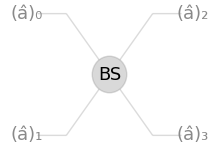
```mathematica
-Graphics--Graphics-
```

The quantum beam splitter is described as a device with two input modes and two output modes. The creation operators between the input and output modes can be related with a linear transformation , that depends on the complex reflectance and transmittance coefficients:

((â)_2
(â)_3)=(t' | r
r' | t)((â)_0
(â)_1)

with |r'|=|r|, |t'|=|t|, |r|^2+|t|^2=1, r^*t'+r' t^*=0 ,  r^*t+r' t'^*=0

Define the transformation matrix:

```mathematica
transf =({{t', r}, {r', t}})
```

(t' | r
r' | t)

Calculate the output modes in terms of in the input modes:

```mathematica
{a2,a3}= transf . {a0 , a1};
{a2d,a3d}=transf*. {SuperDagger[a0], SuperDagger[a1]};
```

Compute all the commutators for the output modes:

```mathematica
res =FullSimplify[(redu@*Commutator) @@@Subsets[{a2,a2d,a3,a3d},{2}]]
```

{Abs[r]^2+Abs[t']^2,0,t' Conjugate[(r')]+r Conjugate[t],-r' Conjugate[(t')]-t Conjugate[r],0,Abs[r']^2+Abs[t]^2}

Enforcing the values of the commutation relations, we get the relations for the complex coefficients (also called reciprocity relations):

```mathematica
And@@Thread[res=={1,0,0,0,0,1}]
```

Abs[r]^2+Abs[t']^2==1∧t' Conjugate[(r')]+r Conjugate[t]==0∧-r' Conjugate[(t')]-t Conjugate[r]==0∧Abs[r']^2+Abs[t]^2==1

#### Types of Beam Splitters

A general expression for a beam splitter matrix (that relates input and output modes) can be expressed in terms of reflection, transmission and global phases(ϕ_r, ϕ_t,ϕ_g) and the mixing angle (θ) as:

e^(ⅈ ϕ_g)(sin(θ)e^(ⅈ ϕ_t) | cos(θ)e^(-ⅈ ϕ_r)
cos(θ)e^(ⅈ ϕ_r) | -sin(θ)e^(-ⅈ ϕ_r))    {θ, ϕ_t, ϕ_r, ϕ_g} ∈ ℝ

Define the general beam-splitter as a QuantumOperator:

```mathematica
GeneralBS = QuantumOperator[ⅇ^(ⅈ ϕg)({{Sin[θ] ⅇ^(ⅈ ϕt), Cos[θ] ⅇ^(-ⅈ ϕr)}, {Cos[θ] ⅇ^(ⅈ ϕr), -Sin[θ] ⅇ^(-ⅈ ϕt)}}),"Parameters"->{θ,ϕg,ϕr,ϕt}];
```

Check the operator is unitary , a condition that represents energy conservation:

```mathematica
Simplify[SuperDagger[GeneralBS]@GeneralBS,{θ,ϕt,ϕr,ϕg}∈Reals]
```

00+11

In practice, two kinds of beam-splitter are used more frequently: dielectric and symmetric beam-splitters. To get a 50:50  balanced beam-splitter set  θ = π/4, and the other phases are set to particular values that depend on the type of beam splitter

Dielectric BS has the matrix representation (r | t
t | -r) , setting ϕ_g,ϕ_r,ϕ_t=0

Set the 50/50 case:

```mathematica
GeneralBS[π/4,0,0,0];
```

See the matrix representation:

```mathematica
%["Matrix"]//MatrixForm
```

(1/(√2) | 1/(√2)
1/(√2) | -1/(√2))

A balanced, lossless dielectric beam splitter (BS) has a scattering matrix that is equivalent to the Hadamard gate due to a combination of energy conservation (unitarity) and spatial symmetry

```mathematica
GeneralBS[π/4,0,0,0]==QuantumOperator["H"]
```

True

Symmetric BS, has the matrix representation (r | ⅈ t
ⅈ t | r), setting ϕ_g=π/2, ϕ_r=0, ϕ_t=-π/2

Set the 50/50 case:

```mathematica
GeneralBS[π/4,π/2,0,-π/2];
```

See the matrix representation:

```mathematica
%["Matrix"]//MatrixForm
```

(1/(√2) | ⅈ/(√2)
ⅈ/(√2) | 1/(√2))

Dielectric BS in terms of the reflectivity r :

```mathematica
bs1 = GeneralBS[ArcSin[r],0,0,0];
```

Associated matrix such that t =√(1-r^2):

```mathematica
(Normal[bs1["Matrix"]]/. √(1-r^2)->t)//MatrixForm
```

(r | t
t | -r)

The matrix representations of the previous cases of beam splitters consider real parameters, because the complex dependency comes from the chosen values of the phases

### Digression: Polarization of a Photon

The polarization degrees of freedom of a photon can be described in a quantum two-level system, which follows the same mathematical structure as the classical description with Jones vectors.

Define the polarization photon basis, the most widely used is the one in terms of the horizontal and vertical polarization states:

```mathematica
polBasis = QuantumBasis[{"H","V"}];
```

Show the basis:

```mathematica
polBasis//TraditionalForm
```

<|H→{1,0},V→{0,1}|>

An alternative basis is working in the diagonal and antidiagonal basis, which is equivalent to the X operator eigenstates:

```mathematica
diagPolBasis =QuantumBasis@AssociationThread[{"D","A"}->QuantumBasis["X"]["Elements"]];
```

Change of basis in the Wolfram Quantum Framework:

```mathematica
QuantumState["+",polBasis]
```

1/(√2)H+1/(√2)V

```mathematica
QuantumState[%,diagPolBasis]
```

D

Analogous to standard qubits(Bloch sphere) the states of polarization can be represented in the Poincaré sphere, where pure states of polarization sit on the surface of the sphere

Let’s show an example of polarization projection

We will project the first photon of the |ψ^-⟩ state to diagonal polarization, and plot the amplitudes in a two-photon diagonal-antidiagonal basis

Create the state:

```mathematica
psiminus = QuantumState["PsiMinus",polBasis]
```

1/(√2)HV-1/(√2)VH

Project the first photon (this means using a polarizer or projector |D⟩ ⟨D|):

```mathematica
projectionD =QuantumState["0",diagPolBasis]["Projector"]@QuantumState["PsiMinus",polBasis]
```

-1/2DH+1/2 DV

Use "AmplitudesPlot", only |DA⟩ has nonzero amplitude:

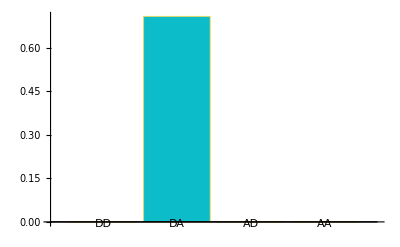

```mathematica
QuantumState[projectionD,QuantumBasis[{diagPolBasis,diagPolBasis}]]["AmplitudesPlot",ChartLegends->Automatic]
```

#### Wave plates

To change the state of polarization we can use wave plates made of birefringent materials, which possess two distinct refractive indices corresponding to the crystal’s “fast” and “slow” optical axes. When a light enters the material, its electric field splits into two orthogonal components that travel along these axes at different speeds. This velocity difference introduces a phase shift, or retardation, between the two light waves. As the components exit the crystal and recombine, this accumulated phase difference alters the overall orientation of the electric field, resulting in a completely new state of polarization

The two most common realizations of these devices are half-wave plates(λ/2 shift) and quarter-wave plates(λ/4 shift), each manufactured to a precise thickness to achieve a specific retardation between electric field components.

When a wave plate is positioned at an angle 0°, meaning its fast and slow optical axes are perfectly aligned horizontally  and vertically its matrix representation is perfectly diagonal. For the case that the vertical one is aligned with the slow axis it will acquire a phase delay Γ

```mathematica
DiagonalMatrix[{1,ⅇ^(ⅈ Γ)}]//MatrixForm
```

(1 | 0
0 | ⅇ^(ⅈ Γ))

Picking values such as Γ=π we get a half-wave plate, and with Γ=π/2 we get a quarter-wave plate

We will show half-wave plate and quarter-wave plate (HWP and QWP) definitions in the H and V polarization basis. To get the matrices at some angle θ (where fast and slow axes do not align with horizontal and vertical), we rotate the frame so we can apply the matrix representing θ = 0 , and finally we rotate back the frame so

U(θ)= R(θ)U(0)R(-θ)

Half-wave plate at an angle θ:

```mathematica
TraditionalForm[mat1=RotationMatrix[θ].{{1,0},{0,ⅇ^(ⅈ π)}}.RotationMatrix[-θ]//Simplify]
```

(cos(2 θ) | sin(2 θ)
sin(2 θ) | -cos(2 θ))

Quarter-wave plate at angle θ:

```mathematica
TraditionalForm[mat2 =RotationMatrix[θ].{{1,0},{0,ⅇ^(ⅈ π/2)}}.RotationMatrix[-θ]//Simplify]
```

(cos^2(θ)+ⅈ sin^2(θ) | (1-ⅈ) sin(θ) cos(θ)
(1-ⅈ) sin(θ) cos(θ) | sin^2(θ)+ⅈ cos^2(θ))

Wrapping matrices in QuantumOperator:

```mathematica
HWP = QuantumOperator[mat1,polBasis,"Parameters"->θ];
QWP = QuantumOperator[mat2,polBasis,"Parameters"->θ];
```

Common single-qubit gates can be implemented by particular angles:

```mathematica
HWP[π/4]==QuantumOperator["X"]
```

True

```mathematica
HWP[π/8]==QuantumOperator["H"]
```

True

Transforming |H⟩ polarization to |V⟩:

```mathematica
QuantumState["0",polBasis]
```

H

```mathematica
HWP[π/4][%]
```

V

In general, any operator that belongs to SU(2) in polarization space can be realized with a sequence of QWP-HWP-QWP operations.

### Evolution of states in beam-splitters

In this section, we will explore the dynamical evolution and resulting properties of various quantum states as they propagate through a beam splitter. By applying our derived operator relations to specific input fields,ranging from classical-like coherent states to strictly non-classical Fock states.

Define the output modes:

```mathematica
{a2,a3} = Table[AnnihilationOperator[{i}],{i,2}];
```

Define a symmetric 50:50 beam splitter:

```mathematica
balancedBS =GeneralBS[π/4,π/2,0,-π/2];
```

We calculate the inverse matrix because in this case we find input modes in terms of output modes (Heisenberg-like evolution of the operators):

```mathematica
{a0,a1} = Inverse@balancedBS["Matrix"].{a2,a3};
```

Prove the evolution of a one-photon state |0⟩_0|1⟩_1 →^BS 1/(√2)(|0⟩_2|1⟩_3+ⅈ |1⟩_2|0⟩_3):

```mathematica
TraditionalForm[onePhotonEvolve = SuperDagger[a1][]]
```

1/(√2)01+ⅈ/(√2)10

The output state results in a entangled state see QuantumEntanglementMonotone (default metric is “Concurrence”):

```mathematica
QuantumEntanglementMonotone[onePhotonEvolve,{1,2}]
```

1

If we put one photon in each of the input ports, the two photons emerge together. That is explained by interference when the photons are indistinguishable (Hong–Ou–Mandel effect)

State will evolve as |1⟩_0|1⟩_1 →^BS ⅈ/(√2)(|0⟩_2|2⟩_3+ⅈ |2⟩_2|0⟩_3):

```mathematica
TraditionalForm[twoPhotonEvolve = SuperDagger[a0]@SuperDagger[a1][]]
```

ⅈ/(√2)02+ⅈ/(√2)20

There is also possible to adopt a Schrodinger picture approach and for the 50:50 symmetric beam splitter we have the unitary

Û=exp(ⅈ π/4((â)_0^†(â)_1+(â)_0(â)_1^†))

Or use the Heisenberg picture in the more rigorous way in terms of the unitary operator Û:

(â)_2=(Û)^†(â)_0 U

(â)_3= (Û)^†(â)_1 U

Define the spatial modes:

```mathematica
{{a0,a1},{a2,a3}} = Table[AnnihilationOperator[{i}],2,{i,2}];
```

Calculate the unitary operator representing the beam-splitter:

```mathematica
U = QuantumOperator[MatrixExp[ⅈ π/4 N[(SuperDagger[a0]@a1+a0@SuperDagger[a1])]],"Label"->"BS"];
```

Express the input modes in terms of the output modes using Heisenberg picture, note the order of U and U^† and “Ordered” serves for identity padding so dimensions match:

```mathematica
{a0Heis,a1Heis}=(U@(N[#]["Ordered",1,2])@SuperDagger[U])&/@{a2,a3};
```

Calculate the evolution of (|0⟩)_0|1⟩_1:

```mathematica
RootApproximant/@SuperDagger[a1Heis][]["Amplitude"]
```

<|01→1/(√2),10→ⅈ/(√2)|>

Representing the evolution as a circuit for a Schrodinger picture approach:

```mathematica
photonEvolve = QuantumCircuitOperator[{FockState[{1,1}],U}];
```

See the diagram:

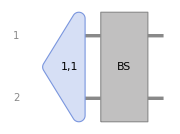

```mathematica
photonEvolve["Diagram",ImageSize->Small]
```

Schrodinger picture evolution:

```mathematica
RootApproximant/@photonEvolve[]["Amplitude"]
```

<|02→ⅈ/(√2),20→ⅈ/(√2)|>

In the QuantumFramework we have  BeamSplitterOperator for doing Schrodinger picture evolution (recurrence method is preferred for symbolic numbers)

```mathematica
balancedsymmetric = BeamSplitterOperator[{π/4,π/2},Method->"Recurrence"];
```

We get the same result:

```mathematica
balancedsymmetric@FockState[{1,1}]//TraditionalForm
```

ⅈ/(√2)02+ⅈ/(√2)20

Now let’s try using a coherent state in the input port one |0⟩_0|α⟩_1 using the definition of displacement operator (D̂)_1(α)=exp(α (â)_1^†-α^* (â)_1)

Numerical amplitude:

```mathematica
αcoh = RandomReal[{1,1.5}]Exp[ⅈ RandomReal[{0,2π}]];
```

Evolve the operators:

```mathematica
{a0,a1} = Inverse@balancedBS["Matrix"].{a2,a3};
```

Output state:

```mathematica
cohBS = MatrixExp[(αcoh a1["Dagger"]-αcoh* a1)][]//Chop;
```

The entanglement monotone is really close to zero, so it is a product state (not entangled):

```mathematica
QuantumEntanglementMonotone[cohBS,{{1},{2}}]
```

0

The theoretical result represents that a coherent state resembles a classical field that divides evenly in a 50:50 BS (average photon number |α|^2/2 in each output mode and phase shift π/2 for the reflected wave)

(|0⟩_0|α⟩_1→^BS|(ⅈ α)/(√2)⟩)_2(|α/(√2)⟩)_3

Product state:

```mathematica
productState =QuantumTensorProduct@@(CoherentState[]/@({ⅈ αcoh,αcoh}/√2));
```

Evaluate how similar the states are, should be really close to 1:

```mathematica
QuantumSimilarity[cohBS,productState,"Fidelity"]
```

1.

Individual amplitudes have numerical error though, the ones that have bigger numerical error are mostly related to the edge effects of truncation:

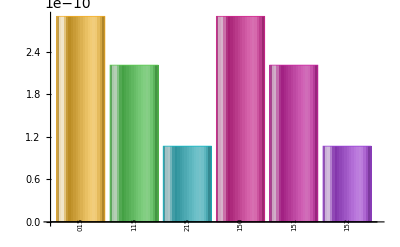

```mathematica
(productState-cohBS)["AmplitudePlot",]
```

Also, the beam splitter causes the transformation that N photons are binomially distributed over the two modes

Let’s verify that for a particular N:

```mathematica
Np = 8;
```

Output state:

```mathematica
outstate = balancedsymmetric[FockState[{0,Np}]]
```

1/16 08+ⅈ/(4 √2)17-(√7)/826-1/4 ⅈ √(7/2)35+(√(35/2))/8 44+1/4 ⅈ √(7/2)53-(√7)/862-ⅈ/(4 √2)71+1/16 80

Probability plot of the output state:

```mathematica
p1 =outstate["ProbabilityPlot",AxesLabel->{"States","Probability"}];
```

Binomial distribution with parameters N_p and p = 0.5:

```mathematica
p2=DiscretePlot[PDF[BinomialDistribution[Np,0.5],k-1],{k,1,Np+1},PlotStyle->{Black,PointSize[0.015]}];
```

Show the result:

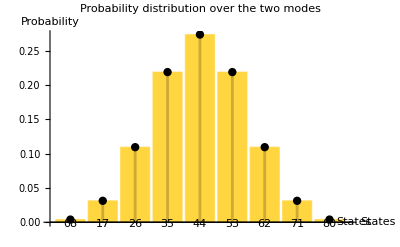

```mathematica
Show[p1,p2,]
```

### Single-Photon Mach–Zehnder Interferometer

Let’s consider the widely used Mach-Zehnder interferometer for the single photon case. The interferometer consists of  two beam-splitters and a phase shift in one of the arms. We can represent the arrangement in the following diagram:

Set up a small truncation size:

```mathematica
SetFockSpaceSize[3];
```

Now we use a dielectric beam-splitter:

```mathematica
dielectricBS =BeamSplitterOperator[{π/4,0}];
```

Phase shift operator:

```mathematica
phase = PhaseShiftOperator[ϕ];
```

Circuit representation of the Mach-Zehnder interferometer arrangement:

```mathematica
MZI =QuantumCircuitOperator[{dielectricBS,phase,dielectricBS}];
```

See the diagram:

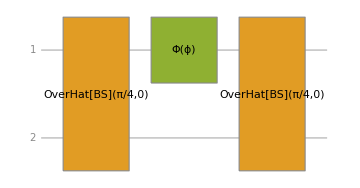

```mathematica
MZI["Diagram","GateBackgroundStyle"->]
```

Calculate the output probabilities:

```mathematica
probs =List@@MZI[FockState[{0,1}]]["Probability"]
```

{(Abs[1/2-ⅇ^(ⅈ ϕ)/2]^2)/(Abs[1/2-ⅇ^(ⅈ ϕ)/2]^2+Abs[-1/2-ⅇ^(ⅈ ϕ)/2]^2),(Abs[-1/2-ⅇ^(ⅈ ϕ)/2]^2)/(Abs[1/2-ⅇ^(ⅈ ϕ)/2]^2+Abs[-1/2-ⅇ^(ⅈ ϕ)/2]^2)}

Simplified probabilities:

```mathematica
simplifiedProbs =Simplify[ComplexExpand[probs],ϕ∈Reals]//TrigReduce
```

{1/2 (1-cos(ϕ)),1/2 (cos(ϕ)+1)}

Plotting probabilities at the detectors:

```mathematica
Plot[Evaluate@MapThread[Callout[#1,#2,Right]&,{simplifiedProbs,{"D1","D2"}}],{ϕ,0,6Pi},
]
```

-Graphics-

Experimentally, this clearly demonstrates wave particle duality: wave-like behavior is seen because an interference pattern emerges and particle-like behavior is evident from the discrete detection events. The pattern builds up progressively as many individual photons pass through the interferometer.

### Hanbury Brown Twiss (HBT) effect

The second-order coherence g^(2) classifies a light source by how its photons arrive bunched, uncorrelated, or antibunched. As written it is a single-mode quantity, and that is a problem for an experiment, because it asks for two photodetections at the same place at the same instant. One detector cannot register two simultaneous clicks, the second photon has nothing left to absorb it.

Hanbury Brown and Twiss removed the obstacle by splitting the beam. Send the source into one port of a balanced beam splitter, leave the other port empty, and put a detector in each output arm. What the pair of detectors measures is a cross correlation between two spatially separated modes, and that quantity is not merely proportional to the single-mode g^(2), it is equal to it.

The reason is worth seeing, because it is the vacuum port that makes it work. Write the source mode as a and the empty port as b. A balanced splitter sends each output to an equal-weight combination of the inputs, a_2=(a+b)/√2 and a_3=(a-b)/√2. Since a and b commute, the coincidence operator collapses to a_2^†a_3^†a_3 a_2=1/4(a^†a^†-b^†b^†)(a a-b b) and on a state |ψ⟩⊗|0⟩ every term carrying b  dies against the vacuum. The arm intensities halve, ⟨n_2⟩=⟨n_3⟩ =1/2⟨n⟩, so the two factors of one half in the denominator cancel the one quarter in the numerator exactly

So we have the equality:

g_23^(2)(0)=⟨a_2^†a_3^†a_3 a_2⟩/(⟨n_2⟩⟨n_3⟩)=(1/4⟨a^†a^†a a⟩)/(1/2⟨n⟩ · 1/2⟨n⟩)⟨a^†a^†a a⟩/(⟨a^†a⟩^2)=g^(2)(0)

Let’s verify this computationally, set up a truncation size:

```mathematica
SetFockSpaceSize[15];
```

Define a balanced beam-splitter and the spatial modes operators:

```mathematica
bs=BeamSplitterOperator[{π/4.,0.}];
a2=AnnihilationOperator[{1}];
a3=AnnihilationOperator[{2}];
```

Number operators and the correlation operator:

```mathematica
n2=SuperDagger[a2]@a2;
n3=SuperDagger[a3]@a3;
corr=SuperDagger[a2]@SuperDagger[a3]@a3@a2;
```

Expectation value:

```mathematica
expect[qs_,op_]:=Tr[op[qs["Operator"]]]
```

HBT correlation function:

```mathematica
hbt[source_QuantumState]:=Block[{out=bs[QuantumTensorProduct[source,FockState[0]]]},Chop[Re[N[expect[out,corr]/(expect[out,n2] expect[out,n3])]]]]
```

Define a list of test states with different statistics, Fock states |1⟩,|2⟩,|3⟩, a coherent state and a thermal state:

```mathematica
states = Join[Array[FockState,3],{CoherentState[][1.0],ThermalState[0.7]}];
```

Show the correlator from the HBT effect at τ=0 coincides with G2Coherence:

```mathematica
With[{labels={"|1⟩","|2⟩","|3⟩","coherent α = 1","thermal n^— = 0.7"}},TableForm[Transpose[{labels,hbt/@states,G2Coherence/@states}],TableHeadings->{None,{"source","HBT g2(0)","G2Coherence"}}]]
```

source | HBT g2(0) | G2Coherence
|1⟩ | 0 | 0
|2⟩ | 0.5 | 1/2
|3⟩ | 0.666667 | 2/3
coherent α = 1 | 1. | 1.
thermal n^— = 0.7 | 1.99936 | 1.99936

### Interference of coherent states

Let’s analyze the interferometry of coherent states in a Mach–Zehnder interferometer. We should expect similar results as using classical light, we will follow a Schrodinger picture evolution approach

Set up parameters:

```mathematica
SetFockSpaceSize[30];
αcoh = 1.8Exp[I RandomReal[{0,2Pi}]];
```

Balanced symmetric BS:

```mathematica
balancedsymmetric = BeamSplitterOperator[{π/4.,π/2.}];
```

MZI interferometer operator (phase shift θ in second arm):

```mathematica
MZI =balancedsymmetric@PhaseShiftOperator[θ,{2}]@balancedsymmetric;
```

Initial state:

```mathematica
init =QuantumTensorProduct[ FockState[0],CoherentState[][αcoh]];
```

Output state:

```mathematica
out = QuantumState[MZI[init],"Parameters"->θ];
```

Evidently the resulting state is a product state, zero entanglement monotone:

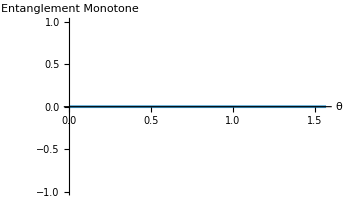

```mathematica
Plot[QuantumEntanglementMonotone[out[θ],{{1},{2}},"Concurrence"],{θ,0,π/2},AxesLabel->{"θ","Entanglement Monotone"}]
```

It can be shown that the analytical expression for the evolution is

(|0⟩_0|α⟩_1→^MZI|(ⅈ(e^(ⅈ θ)+1)α)/2⟩)_c(|((e^(ⅈ θ)-1)α)/2⟩)_d

Product state analytical:

```mathematica
product =QuantumState[QuantumTensorProduct@@CoherentState[]/@{(ⅈ(1+ⅇ^(ⅈ θ))αcoh)/2,(( ⅇ^(ⅈ θ)-1)αcoh)/2},"Parameters"->θ];
```

Sample angles:

```mathematica
phases = N@Subdivide[0,π/2,25];
```

Compare results, empty “AmplitudeList” represent states are numerically the same up the chosen precision:

```mathematica
Quiet[Chop[(out[#]-product[#]),10^-9]["AmplitudeList"]&/@phases]
```

{{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{}}

Phase shift θ can be measured by subtracting the intensities from two detectors, D_1 and D_2. That can be represented by ⟨Ô ⟩ with Ô=(ĉ)^†ĉ-(d̂)^†d̂  the number difference operator(ĉ and d̂ output modes). This is simple to calculate, because the mean of the number operator on a coherent state is just the magnitude of the complex amplitude squared:

Output modes:

```mathematica
{c,d}= Array[AnnihilationOperator[{#}]&,2];
```

Current operator:

```mathematica
Ocurrent = SuperDagger[c]@c -SuperDagger[d]@d;
```

The mean of the Ô operator can be calculated exactly(assuming no truncation) for the tensor product coherent state, since the Ô operator has number operator parts that act separately on each mode:

```mathematica
OmeanSymbolic = FullSimplify[Abs[(ⅈ (ⅇ^(ⅈ θ)+1)α)/2]^2-Abs[((ⅇ^(ⅈ θ)-1)α)/2]^2,Element[θ,Reals]]
```

α Conjugate[α] cos(θ)

Current expectation using the defined states and operators in terms of the parameter θ:

```mathematica
currentMean =Simplify[Chop[(SuperDagger[out[θ]]@Ocurrent@out[θ])["Scalar"]],θ∈Reals];
```

We see it has the same form as the previous calculation, where the coefficient is α α*. Of course this is approximate, and the result will depend how good the coherent states are represented in the truncated space:

```mathematica
Chop[FullSimplify[currentMean]]
```

3.24 cos(θ)

```mathematica
Abs[αcoh]^2
```

3.24

We can recover θ based on the symbolic truncated Fock space expression, of course this is just showing the equivalence in a computational manner, but real measurements will not be perfect:

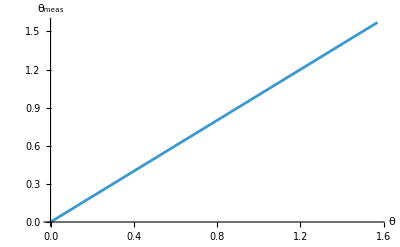

```mathematica
Plot[ArcCos[{Re@currentMean}/Abs[αcoh]^2],{θ,0,π/2},AxesLabel->{"θ"," θ_meas"}]
```

We observe the result analogous to classical coherent light, but coherent states are still quantum states that possess quantum mechanical fluctuations. Using error propagation, the uncertainty of phase measurement is

Δθ=(Δ Ô)/(|(d ⟨Ô⟩)/(d θ)|)=1/(√(n̄)|sin(θ)|)

which is optimal or minimum for odd multiples of π/2. That is the best result with classical-like states determining a standard quantum limit. It is possible to beat that limit using non-classical light. A good example of that is discussed in large-scale interferometers to detect gravitational waves (LIGO).

### Fock space and polarization joint basis

One may initially think that to represent Fock space occupation with polarization is enough to consider the tensor product {H,V}⊗ {0,1,2,3…n}

Tensor the basis (n=3):

```mathematica
QuantumBasis[{polBasis,4}]
```

<|H0→(1 | 0 | 0 | 0
0 | 0 | 0 | 0),H1→(0 | 1 | 0 | 0
0 | 0 | 0 | 0),H2→(0 | 0 | 1 | 0
0 | 0 | 0 | 0),H3→(0 | 0 | 0 | 1
0 | 0 | 0 | 0),V0→(0 | 0 | 0 | 0
1 | 0 | 0 | 0),V1→(0 | 0 | 0 | 0
0 | 1 | 0 | 0),V2→(0 | 0 | 0 | 0
0 | 0 | 1 | 0),V3→(0 | 0 | 0 | 0
0 | 0 | 0 | 1)|>

But what happens when the state we want to represent is exactly 2 horizontal polarized photons and one vertically polarized photon?

The state |H⟩⊗|3⟩ means i have 3 photons and all are horizontal polarized. The state 1/(√2)(|H⟩⊗|2⟩+|V⟩⊗|1⟩) is quantum superposition, which means i can have 2 horizontal photons OR one vertical photon. And the state 1/(√2)(|H⟩+|V⟩)⊗ |3⟩ just means i have 3 photons and are all diagonal polarized. We already see the mathematical structure does not allow a complete freedom of the state we can specify,  unless we specify the tensor product of Hilbert spaces as ℋ = ℋ_H⊗ℋ_V

So a way to implement this is to specify two occupation numbers n_H and n_V corresponding to horizontal and vertical polarizations. Of course we obtain the vacuum when n_H=0 and n_V=0

Let’s start just allowing some particular polarization, show the states for horizontal polarization:

```mathematica
SetFockSpaceSize[10];
```

```mathematica
PolarizationNBasis[3,H]["Association"]//Keys//TraditionalForm
```

{0_H,1_H,2_H}

Or vertical polarization:

```mathematica
PolarizationNBasis[5,V]["Association"]//Keys//TraditionalForm
```

{0_V,1_V,2_V,3_V,4_V}

If we fix the maximum number of photons to n, the joint basis of photons with polarization has dimension of ((n + 1)(n + 2))/2, here size is n+1 (to include 0)

Define Fock polarization basis states with a particular size:

```mathematica
nTrunc =4;
basis = FockPolarizationBasis[nTrunc];
```

Show all the possible states:

```mathematica
basis["Association"]//Keys//TraditionalForm
```

{0_H0_V,0_H1_V,0_H2_V,0_H3_V,1_H0_V,1_H1_V,1_H2_V,2_H0_V,2_H1_V,3_H0_V}

Check the dimension:

```mathematica
basis["Dimension"]== (nTrunc(nTrunc+1))/2
```

True

Annihilation operators associated to horizontal and vertical polarizations:

```mathematica
aH = AnnihilationOperatorPolarization["H",$FockSize];
aV = AnnihilationOperatorPolarization["V",$FockSize];
```

Define the vacuum:

```mathematica
vacuum = QuantumState["0",FockPolarizationBasis[$FockSize]]
```

0_H0_V

“Kill” the vacuum:

```mathematica
aH@vacuum
```

0

```mathematica
aV@vacuum
```

0

Test (â)_V|0_H,1_V⟩:

```mathematica
s =QuantumState["1",FockPolarizationBasis[$FockSize]]
```

0_H1_V

```mathematica
aV@s
```

0_H0_V

Test (â)_H^†|0_H,1_V⟩:

```mathematica
SuperDagger[aH]@s
```

1_H1_V

When dealing with multiple indistinguishable bosons, their total wavefunction must be perfectly symmetric under particle exchange. If you tried to use a tensor product of single-photon polarization states for an N-photon system, you would have to  symmetrize sums over all possible particle permutations.The mode-occupation basis |n_H,n_V⟩ automatically handles this. Because creation operators for different modes commute, the order in which you create the photons does not matter

```mathematica
Commutator[aH,aV]
```

0

```mathematica
SuperDagger[aH]@SuperDagger[aV][]
```

1_H1_V

```mathematica
SuperDagger[aV]@SuperDagger[aH][]
```

1_H1_V

One photon state with diagonal polarization can be .08represented as:

```mathematica
1/(√2)(SuperDagger[aH]+SuperDagger[aV])[]
```

1/(√2)0_H1_V+1/(√2)1_H0_V

Which using the naive basis would be |D⟩ ⊗ |1⟩, for this case is trivial since is the n=1 subspace

The two ladders a_H and a_V​ generate the polarization observables themselves, and they do so for any number of photons at once

```mathematica
SetFockSpaceSize[5];
```

```mathematica
aH=AnnihilationOperatorPolarization["H",$FockSize];
aV=AnnihilationOperatorPolarization["V",$FockSize];
```

Take the three Hermitian bilinear that can be formed from polarization modes J_x=1/2(a_H^†a_V+a_V^†a_H), J_y=1/(2ⅈ)(a_H^†a_V-a_V^†a_H), J_z=1/2(a_H^†a_H-a_V^†a_V) together with the total number operator

```mathematica
Jx=1/2 (SuperDagger[aH][aV]+SuperDagger[aV][aH]);
Jy=(SuperDagger[aH][aV]-SuperDagger[aV][aH])/(2 ⅈ);
Jz=1/2 (SuperDagger[aH][aH]-SuperDagger[aV][aV]);
Nop=SuperDagger[aH][aH]+SuperDagger[aV][aV];
```

Check the J_i verify the algebra of angular momentum:

```mathematica
With[{Js={Jx,Jy,Jz}},TraditionalForm[Table[Commutator[Js⟦i⟧,Js⟦j⟧],{i,3},{j,3}]-Table[ⅈ ∑_k^3 Signature[{i,j,k}] Js⟦k⟧,{i,3},{j,3}]]]
```

(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0)

Check the relation of the Casimir invariant J^2:

```mathematica
(Jx@Jx+Jy@Jy+Jz@Jz)==(Nop/2)@(Nop/2+1)
```

True

It is possible to extend the definition of Stokes vector in Poincaré sphere to these states, where instead of the Pauli operators in polarization space we use the J_i operators

Calculate the Stokes vector {⟨J_x⟩,⟨J_y⟩,⟨J_z⟩} for states |2_H,0_V⟩,|0_H,2_V⟩ and |1_H,1_V⟩:

```mathematica
stokes@*ketHV/@{{2,0},{0,2},{1,1}}
```

{{0,0,1},{0,0,-1},{0,0,0}}

Two horizontal photons sit at the north pole, two vertical ones at the south, and one of each sits at the centre. The last of these is already worth noticing: 
|1is a perfectly definite state of the field, yet it points nowhere on the sphere, because the intensities it compares are balanced in every one of the three conjugate pairs.

Calculate degree of polarization of |1_H ,1_V⟩:

```mathematica
DoP[ketHV[{1,1}]]
```

0

Superposing two poles states gives the so called NOON state:

```mathematica
noon = 1/(√2)(ketHV[{2,0}]+ketHV[{0,2}])
```

1/(√2)0_H2_V+1/(√2)2_H0_V

Calculate its Stoke vector:

```mathematica
stokes[noon]
```

{0,0,0}

It is pure, it carries two photons, and its Stokes vector vanishes in all three components, so its degree of polarization is zero. A single photon has nowhere to hide, every pure one-photon state lies on the surface of the sphere with degree of polarization one. From two photons upward, purity and polarization come apart, and a state can be completely known and completely unpolarized at the same time

A wave plate is a rotation generated by one of these operators:

```mathematica
wp=MatrixExp[ (-ⅈ) π/3 Jx];
```

```mathematica
wp["UnitaryQ"]
```

True

To one-photon it does something can be reproduced as a rotation applied to a qubit (which basically was the approach of the digression):

```mathematica
wp[ketHV[{1,0}]]//Simplify
```

-ⅈ/20_H1_V+(√3)/2 1_H0_V

```mathematica
QuantumOperator["RX"[π/3]][]
```

(√3)/2 0-ⅈ/21

But of course for two-photons it does something a qubit cannot show:

```mathematica
wp[ketHV[{2,0}]]//Simplify
```

-1/40_H2_V-1/2 ⅈ √(3/2)1_H1_V+3/4 2_H0_V

```mathematica
stokes[%]
```

{0,-(√3)/2,1/2}

##### Initialization

Load the Quantum Framework:

```mathematica
Needs["Wolfram`QuantumFramework`"]
```

Load the second quantization tools:

```mathematica
Needs["Wolfram`QuantumFramework`SecondQuantization`"]
```

Two mode bosonic operator algebra:

```mathematica
alg=NonCommutativeAlgebra[{"Generators"->FieldVariables[a,{0,1}],
"CommutationRelations"->BosonicRelations[FieldVariables[a,{0,1}]]}];
```

Reduction function:

```mathematica
redu[e_]:=NonCommutativePolynomialReduction[e,alg["CommutationRelations"],alg]
```

Annihilation operator:

```mathematica
a := AnnihilationOperator[]
```

Extra definitions for joint basis:

```mathematica
PolarizationNBasis[size_:$FockSize,pol_]:=QuantumBasis[Table[StringTemplate["\!\(\*SubscriptBox[\(`n`\), \(`pol`\)]\)"][Association["n"->n,"pol"->pol]],{n,0,size-1}]]
```

```mathematica
FockPolarizationBasis[size_:$FockSize]:=QuantumBasis[Flatten[Table[StringTemplate["\!\(\*SubscriptBox[\(`nH`\), \(H\)]\)\!\(\*SubscriptBox[\(`nV`\), \(V\)]\)"][Association["nH"->nH,"nV"->nV]],{nH,0,size-1},{nV,0,size-1-nH}]]]
```

Helper function that returns the pairs of valid occupation numbers:

```mathematica
basisPairs[size_:$FockSize]:=Flatten[Table[{nH,nV},{nH,0,size-1},{nV,0,size-nH-1}],1];
```

Implementation of an annihilation operator with polarization:

```mathematica
AnnihilationOperatorPolarization[pol_String,size_Integer:$FockSize]:=Block[{pairs=basisPairs[size],dim,index,rules},dim=Length[pairs];
index=AssociationThread[pairs->Range[dim]];
rules=Flatten[MapIndexed[With[{nH=#[[1]],nV=#[[2]],i=First[#2]},
Which[
pol==="H"&&nH>=1,
{{index[{nH-1,nV}],i}->Sqrt[nH]},
pol==="V"&&nV>=1,
{{index[{nH,nV-1}],i}->Sqrt[nV]},
True,{}]]&,pairs]];
QuantumOperator[SparseArray[rules,{dim,dim}],FockPolarizationBasis[size]]]
```

Joint Fock-polarization ket, stokes vector, degree of polarization:

```mathematica
ketHV[{nh_,nv_}]:=FockPolarizationBasis[$FockSize]["BasisStates"][[Position[basisPairs[$FockSize],{nh,nv}][[1,1]]]]
```

```mathematica
StokesVec[qs_]:=(SuperDagger[qs]@#@qs)["Scalar"]&/@{Jx,Jy,Jz};
```

```mathematica
DoP[qs_]:=Norm[stokes[qs]]/((SuperDagger[qs]@(Nop/2)@qs)["Scalar"]);
```

Vocabulary

BeamSplitterOperator |   | Operator  that performs evolution of states going
through a beam-splitter in the Schrodinger picture
PhaseShiftOperator |   | Applies a phase factor proportional to the photon number
of the Fock state
QuantumEntanglementMonotone |   | calculates a metric to measure entanglement of a
QuantumState, default metric is “Concurrence”

Exercises

Load the Quantum Framework paclet:

Needs["Wolfram`QuantumFramework`"]
Needs["Wolfram`QuantumFramework`SecondQuantization`"]

Define the basis of circular right |R⟩, and circular left polarization |L⟩ (use any convention):

Solution

QuantumBasis@AssociationThread[{"R","L"}->QuantumBasis["Y"]["Elements"]]

<|"R"→{1/(√2),ⅈ/(√2)},"L"→{1/(√2),-ⅈ/(√2)}|>

Or just passing explicitly the expressions in the basis :

QuantumBasis[<|"R"->1/(√2){1, ⅈ},"L"->1/(√2){1,-ⅈ}|>]

<|"R"→{1/(√2),ⅈ/(√2)},"L"→{1/(√2),-ⅈ/(√2)}|>

Check that the state |3,1⟩ has a uniform distribution after a balanced beam-splitter operation

Solution

BeamSplitterOperator[{π/4.,π/2.}][FockState[{3,1}]]["ProbabilityPlot"]

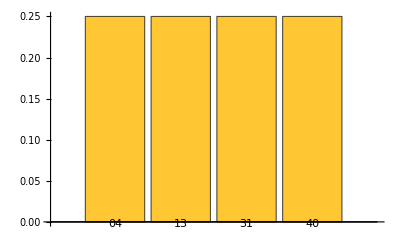

Given the generators 
J_1=1/2(a_0^†a_1+a_1^†a_0),  J_2= 1/2 ⅈ (a_0^†a_1-a_1^†a_0),   J_3=1/2((a^†)_0 a_0-(a^†)_1 a_1)
these generators can describe beam-splitter transformations constructing the unitary
 U(θ) = exp(ⅈ θ J_i). Show the generators satisfy the angular momentum algebra [J_i,J_j] = ⅈ ε_(i j k) J_k.
If we define J_0=1/2(a_0^†a_0+a_1^†a_1) show J_0 commutes with all the generators, and check J^2 = J_0(J_0+1)

Solution

Clear[a0,a1];

Define the J_i operators:

J0 = (a0^†**a0+a1^†**a1)/2;
JList ={(a0^†**a1+a1^†**a0)/2,(a0^†**a1-a1^†**a0)/(2ⅈ),(a0^†**a0-a1^†**a1)/2};

Define all the commutation relations for two modes and the non-commutative variables:

vars = {a0,a1,a0^†,a1^†};

rels = Commutator[#1,#2]-Boole[#2===SuperDagger[#1]]&@@@Subsets[vars,{2}];

Verify the angular momentum algebra:

resComm=Table[NonCommutativePolynomialReduce[Commutator[JList[[i]],JList[[j]]]-I*Sum[Signature[{i,j,k}]*JList[[k]],{k,3}],rels,vars][[-1]],{i,3},{j,3}]

{{0,0,0},{0,0,0},{0,0,0}}

J_0 commutes with all the generators:

```mathematica
Table[NonCommutativePolynomialReduce[Commutator[J0,JList[[i]]],rels,vars][[-1]],{i,3}]
```

{0,0,0}

Verify the relation J^2=J_0(J_0+1):

NonCommutativePolynomialReduce[Sum[Ji**Ji,{Ji,JList}]-J0**(J0+1),rels,vars][[-1]]

0

A polarizing beam-splitter (PBS) is a device that also has two spatial input and output modes but that is sensitive to polarization. Horizontal polarization is transmitted and vertical polarization is reflected, for single photons the PBS can be described in 4-dimensional Hilbert space. Define the QuantumOperator representing the PBS, assume we have diagonal polarization incoming in one input mode , then show the state after the PBS is unpolarized (mixed)

Solution

Define polarization basis:

polBasis = QuantumBasis[{"H","V"}];

Define path basis:

pathBasis = QuantumBasis[{"e_0","e_1"}];

It can be derived that the associated matrix in the joint basis is very similar to a CNOT gate, horizontal polarization keeps the path label but vertical polarization flips it:

PBS = QuantumOperator[(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | ⅈ
0 | 0 | ⅈ | 0),{polBasis,pathBasis}]

"H""e_0""H""e_0"+"H""e_1""H""e_1"+ⅈ"V""e_0""V""e_1"+ⅈ"V""e_1""V""e_0"

Define the initial state:

ψ =QuantumState["+0",{polBasis,pathBasis}]

1/(√2)"H""e_0"+1/(√2)"V""e_0"

We get the expected result ρ_pol=1/2(1 | 0
0 | 1):

QuantumPartialTrace[PBS[ψ],{2}]==QuantumState["UniformMixture",polBasis]

True

Using a balanced beam splitter obtained with J_1 generator, show numerically(for some value of N) that for an input state |N⟩|N⟩ the output state takes the form
|out⟩ = (ⅈ)^N(∑^N)_(k = 0) (Binomial[2k,k] Binomial[2N-2k,N-k] (1/2)^(2N))^(1/2) |2k⟩ |2N - 2k⟩
Do a plot of the joint photon distribution for non zero values

Solution

Define a value of truncation, the value of N and the operators:

SetFockSpaceSize[16];
Np=($FockSize-2)/2;

a0 := AnnihilationOperator[];
a1 := AnnihilationOperator[{2}];

Building the beam-splitter operator:

BSJ1 =MatrixExp[ ⅈ π/2.(a0^†@a1+a0@a1^†)/2];

Output states corresponding to the evolution and the analytical expression:

outState =Chop[BSJ1[FockState[{Np,Np}]]];

analytic =((ⅈ)^Np Sum[√(Binomial[2k,k]Binomial[2Np-2k,Np-k](1/2.)^(2 Np))FockState[{2k,2Np-2k}],{k,0,Np}]);

Check the numerical equality:

Chop[(outState-analytic)["AmplitudeList"]]

{}

Show the probability distribution:

outState["ProbabilityPlot"]

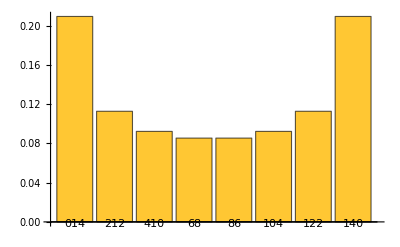

In the limit of N big, the distribution takes the form of the arcsine distribution (up to some scaling):

Plot[PDF[ArcSinDistribution[],x],{x,0,1},PlotRange->{0,2}]

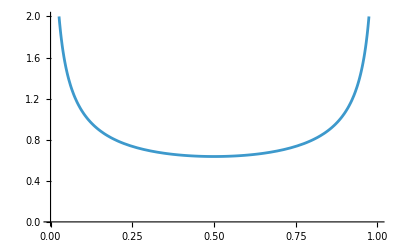

References

Gerry, Christopher C. and Peter. L. Knight. 2005. Introductory Quantum Optics. Cambridge University Press.

Simon, R., and N. Mukunda. 1990. Minimal Three-Component SU(2) Gadget for Polarization Optics. Physics Letters A 143 (4–5): 165–69.

Beck, Mark. 2012. Quantum Mechanics : Theory and Experiment. Oxford University Press.

Loudon, Rodney. 1979. The Quantum Theory of Light. Clarendon Press.

Grangier, P., G. Roger, and A. Aspect. 1986. Experimental Evidence for a Photon Anticorrelation Effect on a Beam Splitter: A New Light on Single-Photon Interferences. Europhysics Letters (EPL) 1 (4): 173–79.